```mathematica
Qfield[x_]:=(({{0, -1}, {1, 0}}).x)/(2π Max[x.x,0.001])
```

```mathematica
Условия задачи
```

```mathematica
ν=(*1/1000*)10^-5;τ=0.01;eps=0.0001;Vinf={1,0};
```

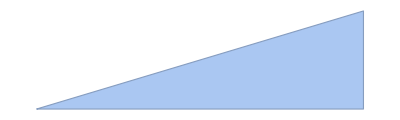

```mathematica
Rdots={{-1,-0.1},{0,0.2},{1,1/2},{1,0.2},{1,-0.1},{0,-0.1}};
Rarea=BoundaryMeshRegion[Rdots,Line[{1,2,3,4,5,6,1}]]
```

```mathematica
Rmids=(RotateLeft@Rdots+Rdots)/2;
Rsides=(RotateLeft@Rdots-Rdots);
rotRsides=RotateLeft@Rsides;
lSides=Table[√(Rsides[[i]].Rsides[[i]]),{i,Length@Rsides}];
```

```mathematica
Rnormals=Transpose@(({{0, -1}, {1, 0}}).Transpose@Rsides);
```

```mathematica
Rnormals=Table[Rnormals[[i]]/(√(Rnormals[[i]].Rnormals[[i]])),{i,Length@Rnormals}];
```

```mathematica
curlDeploy=1.05Rdots;
```

```mathematica
pics={};pics2={};
```

```mathematica
Предварительное составление матрицы и нахождение начальных вихрей
```

```mathematica
L1=Table[Qfield[Rmids[[i]]-curlDeploy[[j]]].Rnormals[[i]],{i,1,Length@Rdots},{j,1,Length@Rdots}];
newGamma=Table[{G[i]},{i,1,Length@Rdots}];
f0=Rnormals.Vinf;
curlsOnPanel={};
curlsInFlow={};
solution=Solve[{L1.newGamma+r==-f0,Sum[newGamma[[i]],{i,Length@newGamma}]==0},Append[First@Transpose@newGamma,r]];
nGammaR=Append[First@Transpose@newGamma,r]/.First@solution;
For[i=1,i≤Length@nGammaR-1,i++,AppendTo[curlsOnPanel,{nGammaR[[i]],curlDeploy[[i]]}]];
minCurl=Max[Abs@nGammaR]*0.001;
```

```mathematica
AllCurls=Join[curlsInFlow,curlsOnPanel];
Vfield=Vinf+Sum[First@AllCurls[[i]]Qfield[{x,y}-Last@AllCurls[[i]]],{i,Length@AllCurls}];
```

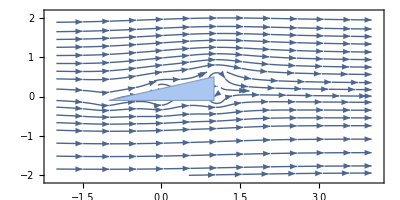

```mathematica
Show[StreamPlot[Vfield,{x,-2,4},{y,-2,2}],Rarea,AspectRatio->1/2]
```

```mathematica
For[k=0,k<100,k++,
AllCurls=Join[curlsInFlow,curlsOnPanel];
f1=ParallelTable[Sum[Rnormals[[i]].Qfield[Rmids[[i]]-Last@AllCurls[[m]]]First@AllCurls[[m]],{m,1,Length@AllCurls}],{i,1,Length@curlDeploy}];
solution=Solve[{L1.newGamma+r==-f0-f1,Sum[newGamma[[i]],{i,Length@newGamma}]==0},Append[First@Transpose@newGamma,r]];
nGammaR=Append[First@Transpose@newGamma,r]/.First@solution;
For[i=1,i≤Length@curlsOnPanel,i++,
If[(Last@curlsOnPanel[[i]]-curlDeploy[[i]]).(Last@curlsOnPanel[[i]]-curlDeploy[[i]])<Min[lSides]^2/16,
curlsOnPanel[[i]][[1]]=curlsOnPanel[[i]][[1]]+nGammaR[[i]];
curlsOnPanel[[i]][[2]]=(Last@curlsOnPanel[[i]]*First@curlsOnPanel[[i]]+curlDeploy[[i]]*nGammaR[[i]])/(First@curlsOnPanel[[i]]+nGammaR[[i]]),
 AppendTo[curlsInFlow,curlsOnPanel[[i]]];(*слабое место, переделать!!!!*)
curlsOnPanel[[i]][[1]]=nGammaR[[i]];
curlsOnPanel[[i]][[2]]=curlDeploy[[i]];
]
(*If[(Last@curlsOnPanel[[i]]-curlDeploy[[i]]).(Last@curlsOnPanel[[i]]-curlDeploy[[i]])<Min[lSides]^2/4,
curlsOnPanel[[i]][[1]]=curlsOnPanel[[i]][[1]]+nGammaR[[i]]
]*)
];
AllCurls=Join[curlsInFlow,curlsOnPanel];

etaR=Table[{x,y}-Rmids[[i]],{i,Length@Rmids}]/eps;(*переделать в соответствии с диссером*)
modEtaR=Table[etaR[[i]].etaR[[i]],{i,Length@Rmids}];
primeR=Table[{x,y}-Last@(AllCurls[[i]]),{i,Length@AllCurls}];
modPrimeR=Table[primeR[[i]].primeR[[i]],{i,Length@AllCurls}];
I2=-Parallelize@Sum[primeR[[i]]/(√modPrimeR[[i]] eps) First@(AllCurls[[i]])Exp[-(√modPrimeR[[i]])/eps],{i,Length@AllCurls}];
I1=Parallelize@Sum[First@(AllCurls[[i]])Exp[-(√modPrimeR[[i]])/eps],{i,Length@AllCurls}];
I3=-Parallelize@Sum[Rnormals[[i]]Exp[-√modEtaR[[i]]],{i,Length@Rnormals}];
(*I3=-Parallelize@Sum[Rnormals[[i]]eps (1-Exp[-(√(Rsides[[i]].Rsides[[i]]))/(2 eps)]),{i,Length@Rnormals}];*)
I0=2π eps^2+Parallelize@Sum[(etaR[[i]].Rnormals[[i]])/modEtaR[[i]](√modEtaR[[i]]+1)Exp[-√modEtaR[[i]]]lSides[[i]],{i,Length@Rnormals}];
Wfield=ν(-I2/I1+I3/I0);
If[Length@curlsInFlow>0,
curlsInFlow=ParallelTable[{First@curlsInFlow[[i]],Last@(curlsInFlow[[i]])+τ (Vfield+Wfield)/.{x->First@Last@(curlsInFlow[[i]])+eps/1000,y->Last@Last@(curlsInFlow[[i]])+eps/1000}},{i,Length@curlsInFlow}];]
curlsOnPanel=ParallelTable[{First@curlsOnPanel[[i]],Last@(curlsOnPanel[[i]])+τ (Vfield+Wfield)/.{x->First@Last@(curlsOnPanel[[i]])+eps/1000,y->Last@Last@(curlsOnPanel[[i]])+eps/1000}},{i,Length@curlsOnPanel}];

(*Ufield[x0_]:=(Vfield+Wfield)/.{x->First@x0,y->Last@x0}*)
(*
curlsOnPanel={};
curlsInFlow={};*)
(*Определяем кандидатов под аннигиляцию и, пока есть такая возможность, без угрызений совести выпиливаем из списка*)
(*curlsToRemove={};*)
For[i=1,i≤Length@curlsOnPanel,i++,If[RegionMember[Rarea,Last@(curlsOnPanel[[i]])] ||Abs@ First@(curlsOnPanel[[i]])<minCurl,curlsOnPanel[[i]][[2]]=curlDeploy[[i]];curlsOnPanel[[i]][[1]]=nGammaR[[i]];];];
(*curlsOnPanel=Delete[curlsOnPanel,curlsToRemove];*)
curlsToRemove={};
For[i=1,i≤Length@curlsInFlow,i++,If[RegionMember[Rarea,Last@(curlsInFlow[[i]])] ||Abs@ First@(curlsInFlow[[i]])<minCurl,AppendTo[curlsToRemove,{i}]];];
curlsInFlow=Delete[curlsInFlow,curlsToRemove];
AllCurls=Join[curlsInFlow,curlsOnPanel];

Vfield=Vinf+Sum[First@AllCurls[[i]]Qfield[{x,y}-Last@AllCurls[[i]]],{i,Length@AllCurls}];
If[Mod[k,5]==0,
AppendTo[pics2,Show[(*ContourPlot[Vfield.Vfield,{x,-2,4},{y,-2,2},PlotLegends->Automatic,PlotRange->{-1,3}],*)StreamPlot[Vfield,{x,-2,4},{y,-2,2}(*,Mesh->5*)],Rarea,AspectRatio->1/2]];
CurlsGraph=Table[Graphics[{White,Disk[Last@AllCurls[[i]],1/20]}],{i,Length@AllCurls}];
AppendTo[pics,Show[ContourPlot[0,{x,-2,4},{y,-2,2}],Rarea,CurlsGraph,AspectRatio->1/2]];]]
```

```mathematica
curlsInFlow
curlsOnPanel
```

{{0.485119,{1.19998,0.314325}},{-0.967022,{1.18281,0.855797}},{-1.87159,{1.73818,0.263854}},{-0.413665,{1.92854,0.0250116}},{-0.617477,{-0.10724,0.477007}},{-0.390752,{1.94954,0.190116}},{-0.219205,{1.36049,0.333859}},{-0.166668,{-0.122151,0.643116}},{-0.34993,{1.66897,0.601703}},{0.0137938,{-0.0145444,0.416821}},{-0.317456,{1.44112,0.73417}},{-0.0997718,{2.06657,0.151598}},{0.364522,{1.49622,0.917571}},{-0.277452,{1.52352,0.598716}},{0.361027,{-0.223357,0.59822}},{0.20903,{2.12924,-0.0322773}},{-0.0306941,{2.05717,-0.0871871}},{0.158302,{1.06581,0.848181}},{0.374944,{1.28089,0.0681559}},{-0.0688848,{1.7181,0.738481}},{-0.869425,{0.570799,1.0119}},{0.0198614,{1.30807,-0.427621}},{-0.964713,{1.86943,0.497675}},{-1.41021,{0.434753,0.593971}},{0.462375,{0.364007,0.82178}},{-2.22588,{-0.743084,0.273774}},{-0.0115239,{-0.608578,0.365422}},{0.623197,{0.60451,1.0542}},{-0.813619,{1.62427,0.7763}},{-0.213524,{1.2922,-0.0214403}},{0.21336,{-0.656863,0.155497}},{-0.116904,{1.53156,0.870248}},{0.457761,{-0.885786,0.417343}},{0.404198,{0.19594,0.328505}},{0.0292738,{1.12013,0.765984}},{0.393092,{-0.944684,0.202402}},{0.65863,{1.14285,-0.0573017}},{0.017118,{1.11161,0.105949}}}

{{-0.732176,{-1.03033,-0.0406188}},{-1.273,{0.0337647,0.249864}},{-0.271924,{1.07315,0.598409}},{0.0280849,{1.05094,0.211349}},{0.0301194,{1.06259,-0.114716}},{0.631718,{0.00138049,-0.100439}}}

```mathematica
Length@curlsOnPanel
```

6

```mathematica
Length@pics
```

20

```mathematica
Export["tester2.gif",pics2]
```

tester2.gif

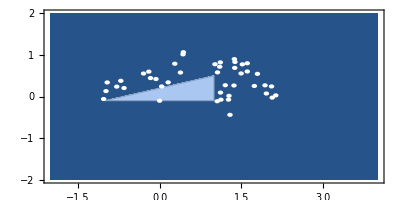

```mathematica
Last@pics
```

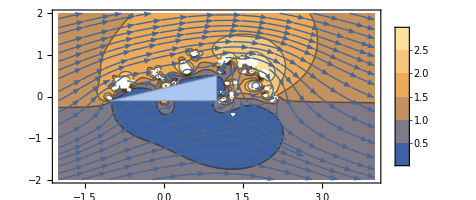

```mathematica
Show[ContourPlot[√(Vfield.Vfield),{x,-2,4},{y,-2,2},PlotLegends->Automatic,PlotRange->{-1,3}],StreamPlot[Vfield,{x,-2,4},{y,-2,2}(*,Mesh->5*)],Rarea,AspectRatio->1/2]
```